WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 21.3044"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

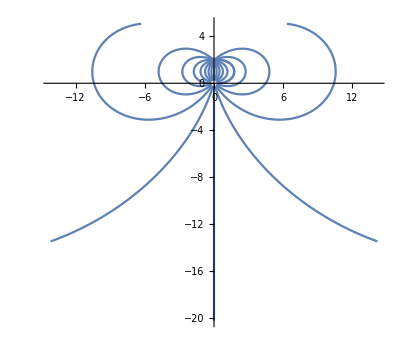

```mathematica
Needs["WSMLink`"];
createStartPoints[x0_,y0_,r_,n_]:=Table[{r*Cos[theta]+x0,r*Sin[theta]+y0},{theta,0,2*Pi,2*Pi/n}];
singleEfieldLineSim[{x0_, y0_}]:= WSMSimulate["EFieldRunner", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}];
multipleEfieldLineSims[x0_,y0_,r_,n_]:=Map[singleEfieldLineSim,createStartPoints[x0,y0,r,n]];
mR1 = multipleEfieldLineSims[0,0,0.25,20];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results=Table[EpPlot[i],{i,1,dmR1}];
Show[results,PlotRange->All]
```